```mathematica
pex[z_,n_]:=Pochhammer[z,n]/n!
lm[n_,t_]:=Sum[t^k/k,{k,1,n}]
```

```mathematica
fl[x_,s_,t_]:=(1/t)Sum[s^k/k MoebiusMu[j]/j lm[x/j/k,t^j],{j,1,x},{k,1,x-t}]
```

```mathematica
fl[10,1,2]
```

761/280

```mathematica
lm[10,3]
```

528153/56

```mathematica
l1[x_,t_]:=(1/t)Sum[MoebiusMu[j]/j lm[x/j,t^j],{j,1,x}]
e1[x_,s_,t_]:=Sum[s^k/k l1[x/k,t],{k,1,x}]
b1[x_,s_,t_]:=Sum[s^k/k ((1/t)Sum[MoebiusMu[j]/j lm[x/k/j,t^j],{j,1,x/k}]),{k,1,x}]
b2[x_,s_,t_]:=(1/t)Sum[s^k/k MoebiusMu[j]/j lm[x/k/j,t^j],{k,1,x},{j,1,x/k}]
b2a[xa_,x_,s_,t_]:=(1/t)Sum[s^r/r MoebiusMu[x/r]/(x/r) lm[xa/r/(x/r),t^(x/r)],{r, Divisors[x]}]
b2a2[xa_,s_,t_]:=Sum[b2a[xa,k,s,t],{k,1,xa}]
```

```mathematica
l1[10,-3]
```

1

```mathematica
b2[10,3,-2]
```

528153/56

```mathematica
Expand[b2[2,s,t]-b2[1,s,t]]
```

s^2/2

```mathematica
Expand@b2a[4,1,s,t]
```

s+(s t)/2+(s t^2)/3+(s t^3)/4

```mathematica
Divisors[2]
```

{1,2}

```mathematica
b2x[x_,s_,t_]:=Table[(1/t)s^k/k MoebiusMu[j]/j lm[x/k/j,t^j],{k,1,x},{j,1,x/k}]//Grid
b2y[xa_,x_,s_,t_]:=Table[(1/t)s^r/r MoebiusMu[(x/r)]/(x/r) lm[xa/r/(x/r),t^(x/r)],{r,Divisors[x]}]
```

```mathematica
b2x[4,s,t]
```

(s (t+t^2/2+t^3/3+t^4/4))/t | -(s (t^2+t^4/2))/(2 t) | -(s t^2)/3 | 0
(s^2 (t+t^2/2))/(2 t) | -(s^2 t)/4 |  | 
s^3/3 |  |  | 
s^4/4 |  |  |

```mathematica
Expand@b2a2[10,s,t]
```

s+s^2/2+s^3/3+s^4/4+s^5/5+s^6/6+s^7/7+s^8/8+s^9/9+s^10/10

```mathematica
Expand@b2[10,s,t]
```

s+s^2/2+s^3/3+s^4/4+s^5/5+s^6/6+s^7/7+s^8/8+s^9/9+s^10/10

```mathematica
b2a[xa_,x_,s_,t_]:=(1/t)Sum[s^r/r MoebiusMu[x/r]/(x/r) lm[xa/x,t^(x/r)],{r, Divisors[x]}]
b2a2[xa_,s_,t_]:=Sum[b2a[xa,k,s,t],{k,1,xa}]
```

```mathematica
Expand@b2a[n,1,s,-s]
```

-(-s)^n s LerchPhi[-s,1,1+n]+Log[1+s]

```mathematica
FullSimplify[(1/t)s^r/r MoebiusMu[x/r]/(x/r) lmm[xa/x,t^(x/r)]]
```

(s^r lmm[xa/x,t^(x/r)] MoebiusMu[x/r])/(t x)

```mathematica
Integrate[t^s,{s,0,x}]
```

(-1+t^x)/Log[t]

```mathematica
Expand@Integrate[t^(s+u),{s,0,x},{u,0,x-s}]
```

1/Log[t]^2-t^x/Log[t]^2+(t^x x)/Log[t]

```mathematica
Expand@Integrate[t^(s+u+v),{s,0,x},{u,0,x-s},{v,0,x-s-u}]
```

-1/Log[t]^3+t^x/Log[t]^3-(t^x x)/Log[t]^2+(t^x x^2)/(2 Log[t])

```mathematica
Expand@Integrate[t^(s+u+v+w),{s,0,x},{u,0,x-s},{v,0,x-s-u},{w,0,x-s-u-v}]
```

1/Log[t]^4-t^x/Log[t]^4+(t^x x)/Log[t]^3-(t^x x^2)/(2 Log[t]^2)+(t^x x^3)/(6 Log[t])

```mathematica
Expand@Integrate[t^(s+u+v+w+y),{s,0,x},{u,0,x-s},{v,0,x-s-u},{w,0,x-s-u-v},{y,0,x-s-u-v-w}]
```

-1/Log[t]^5+t^x/Log[t]^5-(t^x x)/Log[t]^4+(t^x x^2)/(2 Log[t]^3)-(t^x x^3)/(6 Log[t]^2)+(t^x x^4)/(24 Log[t])

```mathematica
ee[x_,k_]:=(-1)^k/Log[t]^k+t^x Sum[(-1)^j  x^j/j!/Log[t]^(k-j),{j,0,k-1}]
```

```mathematica
ee[x,5]
```

t^x (1/Log[t]^5-x/Log[t]^4+x^2/(2 Log[t]^3)-x^3/(6 Log[t]^2)+x^4/(24 Log[t]))-1/Log[t]^5

```mathematica
ee[x,k]
```

(-1)^k Log[t]^-k+(Gamma[k,-x Log[t]] Log[t]^-k)/Gamma[k]

```mathematica
(-1)^k Log[t]^-k+(Gamma[k,-x Log[t]] Log[t]^-k)/Gamma[k]/.x->10/.t->.5/.k->3
```

2.90908

```mathematica
Log[t]^-k((-1)^k +Gamma[k,-x Log[t]]/Gamma[k])/.x->10/.t->.5/.k->3
```

2.90908

```mathematica
Limit[(-1)^k Log[t]^-k+(Gamma[k,-x Log[t]] Log[t]^-k)/Gamma[k],x->Infinity]
```

```mathematica
Limit[ee[x,k]/.t->1/5,x->Infinity]
```

Log[5]^-k

```mathematica
FullSimplify[1/Log[1/t]^k]
```

Log[1/t]^-k

```mathematica
Integrate[t^(s+u),{s,0,x},{u,0,x}]
```

((-1+t^x)^2)/Log[t]^2

```mathematica
Integrate[t^(s+u+v),{s,0,x},{u,0,x},{v,0,x}]
```

((-1+t^x)^3)/Log[t]^3

```mathematica
Limit[((-1+t^x)^3)/Log[t]^3/.t->1/5,x->Infinity]
```

1/Log[5]^3

```mathematica
Limit[((-1+t^x)^k)/Log[t]^k/.t->1/5,x->Infinity]
```

Log[5]^-k

```mathematica
N@Integrate[t^(s+u),{s,0,x},{u,0,x-s}]/.x->120/.t->4/5
```

20.0831

```mathematica
N@Integrate[t^(s+u),{s,0,x},{u,0,x}]/.x->120/.t->4/5
```

20.0831

```mathematica
FullSimplify[Sum[Binomial[z,k]((t^x-1)/Log[t])^k,{k,0,Infinity}]]
```

((-1+t^x+Log[t])/Log[t])^z

```mathematica
Limit[((-1+t^x+Log[t])/Log[t])^z/.t->1/5,x->Infinity]
```

(1+1/Log[5])^z

```mathematica
Table[FullSimplify[D[ee[x,k],x]],{k,0,6}]//TableForm
```

0
t^x
-t^x x
(t^x x^2)/2
-1/6 t^x x^3
(t^x x^4)/24
-1/120 t^x x^5

```mathematica
t^x Sum[Binomial[z,k](x)^k/k!,{k,0,Infinity}]
```

t^x Hypergeometric1F1[-z,1,-x]

```mathematica
Integrate[t^x Hypergeometric1F1[-z,1,-x],{x,0,n}]
```

∫_0^n t^x Hypergeometric1F1[-z,1,-x]ⅆx

```mathematica
Limit[(1+(t^x-1)/Log[t])^z,t->1]
```

(1+x)^z

```mathematica
Limit[((t^x-1)/Log[t])^k,t->1]
```

x^k

```mathematica
f1[q_,k_]:=(1-q^k)/(1-q)
f2[q_,k_]:=(q^k-1)/Log[q]
```

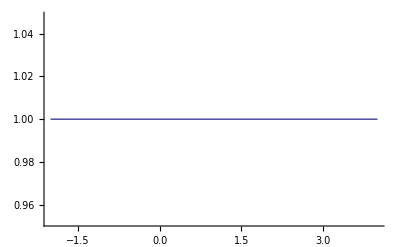

```mathematica
Plot[f1[q,1],{q,-2,4}]
```

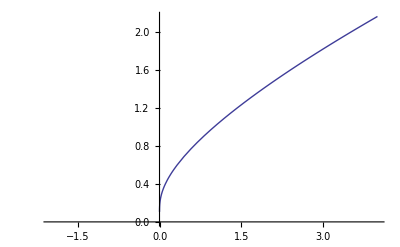

```mathematica
Plot[f2[q,1]/f1[q,1],{q,-2,4}]
```

```mathematica
Sum[(-1)^(k+1)/k((t^x-1)/Log[t])^k,{k,1,Infinity}]
```

Log[(-1+t^x+Log[t])/Log[t]]

```mathematica
Limit[Log[(-1+t^x+Log[t])/Log[t]]/.t->1/5,x->Infinity]
```

Log[1+1/Log[5]]

```mathematica
D[((-1+t^x+Log[t])/Log[t])^z,z]/.z->0
```

Log[(-1+t^x+Log[t])/Log[t]]

```mathematica
Log[-1+t^x+Log[t]]-Log[Log[t]]
```

-Log[Log[t]]+Log[-1+t^x+Log[t]]

```mathematica
FullSimplify@Sum[Binomial[z,k]Log[x]^k/k!,{k,0,Infinity}]
```

LaguerreL[z,-Log[x]]

```mathematica
FullSimplify@Sum[(-1)^(k+1)/k Log[x]^k/k!,{k,1,Infinity}]
```

EulerGamma+Gamma[0,Log[x]]+Log[Log[x]]

```mathematica
Sum[s^t,{s,2,Infinity}]
```

-1+Zeta[-t]

```mathematica
Sum[(s u)^t,{s,2,Infinity},{u,2,Infinity}]
```

$Aborted

```mathematica
FullSimplify[Integrate[(1/E)^Log[x],{x,1,n}],Element[t,Reals]]
```

ConditionalExpression[Log[n],Re[n]≥0||n∉Reals]

```mathematica
FullSimplify[Integrate[t^Log[s],{s,1,x}],Element[t,Reals]]
```

ConditionalExpression[(-1+t^Log[x] x)/(1+Log[t]),Re[x]≥0||x∉Reals]

```mathematica
FullSimplify[Integrate[t^s,{s,0,x}],Element[t,Reals]]
```

(-1+t^x)/Log[t]

```mathematica
Limit[(-1+t^Log[x] x)/(1+Log[t])/.t->1/12,x->Infinity]
```

1/(-1+Log[12])

```mathematica
Limit[(-1+t^Log[x] x)/(1+Log[t]),t->1]
```

-1+x

```mathematica
FullSimplify[Integrate[0^Log[s],{s,1,x}],Element[t,Reals]]
```

∫_1^x 0^Log[s]ⅆs

```mathematica
(-1+t^Log[x] x)/(1+Log[t])/.t->0/.x->2
```

0

```mathematica
FullSimplify[Integrate[t^(Log[s]+Log[u]),{s,1,x},{u,1,x/s}],Element[t,Reals]]
```

ConditionalExpression[(1+t^Log[x] x (-1+(1+Log[t]) Log[x]))/(1+Log[t])^2,Re[x]≥0||x∉Reals]

```mathematica
Expand@((1+t^Log[x] x (-1+(1+Log[t]) Log[x]))/(1+Log[t])^2)
```

1/(1+Log[t])^2-(t^Log[x] x)/(1+Log[t])^2+(t^Log[x] x Log[x])/(1+Log[t])^2+(t^Log[x] x Log[t] Log[x])/(1+Log[t])^2

```mathematica
ah[n_,k_,s_]:=1/(s-1)^k Gamma[k,0,(s-1)Log[n]]/Gamma[k]
ah2[n_,k_,s_]:=1/(-Log[s]-1)^k Gamma[k,0,-(1+Log[s])Log[n]]/Gamma[k]
ah2a[n_,k_,s_]:=1/(Log[1/s]-1)^k Gamma[k,0,(-1+Log[1/s])Log[n]]/Gamma[k]
ah3[x_,t_]:=(1+t^Log[x] x (-1+(1+Log[t]) Log[x]))/(1+Log[t])^2
```

```mathematica
N@ah2[100,2,-2]
```

1946.64+2353.88 ⅈ

```mathematica
N@ah3[100,-2]
```

1946.64+2353.88 ⅈ

```mathematica
FullSimplify[1/(-Log[s]-1)^k Gamma[k,0,-(1+Log[s])Log[n]]/Gamma[k]]
```

(Gamma[k,0,-Log[n] (1+Log[s])] (-1-Log[s])^-k)/Gamma[k]

```mathematica
Limit[(1+t^Log[x] x (-1+(1+Log[t]) Log[x]))/(1+Log[t])^2/.t->1/4,x->Infinity]
```

1/(-1+Log[4])^2

```mathematica
Integrate[(1/E)^(Log[s]+Log[u]),{s,1,x},{u,1,x/s}]
```

ConditionalExpression[Log[x]^2/2,Re[x]≥0||x∉Reals]

```mathematica
Integrate[(1/E)^(Log[s]+Log[u]+Log[v]),{s,1,x},{u,1,x/s},{v,1,x/s/u}]
```

ConditionalExpression[Log[x]^3/6,Re[x]≥0||x∉Reals]

```mathematica
FullSimplify[1/(-1-Log[t])^5]
```

-1/(1+Log[t])^5

```mathematica
Sum[Binomial[z,k]1/(-Log[t]-1)^k Gamma[k,0,(-Log[t]-1)Log[x]]/Gamma[k],{k,0,Infinity}]
```

∑_(k=0)^∞ (Binomial[z,k] Gamma[k,0,(-1-Log[t]) Log[x]] (-1-Log[t])^-k)/Gamma[k]

```mathematica
Sum[s^t,{s,2,Infinity}]
```

-1+Zeta[-t]

```mathematica
bar[t_]:=Sum[t^Log[s],{s,2,Infinity}]
bat[t_]:=Zeta[-Log[t]]-1
```

```mathematica
bar[E^-2]
```

-1+π^2/6

```mathematica
Zeta[2]-1
```

-1+π^2/6

```mathematica
bat[E^-2]
```

-1+π^2/6

```mathematica
Integrate[t^Log[s],{s,1,x}]
```

ConditionalExpression[(-1+t^Log[x] x)/(1+Log[t]),Re[x]≥0||x∉Reals]

```mathematica
Limit[(-1+t^Log[x] x)/(1+Log[t])/.t->1/5,x->Infinity]
```

1/(-1+Log[5])